## Modèle TBR

### Paramètres connues du système

```mathematica
L=1 (*m*); (*hauteur du réacteur*)
d=0.18 (*m*);(*diamètre de la colonne*)
Ω= Pi (d/2)^2(*m.b2*); (*surface de la colonne*)
dp=2.5 10^-2(*m*); (*diamètre éléments de garnissage*)
Ap=312 (*m.b2int.G-L/m.b3column*);

Qgin=(50. 10^-6)/60 (*m.b3/s*) ;(*débit de gaz entrant dans le réacteur*)
Qlin=(4.5 10^-3)/60(*m.b3/s*); (*débit de liquide entrant dans le réacteur*)

Rg=8.314(*kg m.b2 s^-2 K^-1 mol^-1*); (*constante gaz parfait*)
Tin=25+273.15 (*K*); (*température de travail*)
Pin=101325(*Pa*); (*pression de travail*)
Patm=1(*atm*);
gz=9.81 (*m/s.b2*); (*acc gravité*)

Dco2l=3 10^-5 Exp[-3096/Tin] (*m^2/s*); (*coef diffusion CO2 dans l'eau*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)

Dh2l=5.13 10^-9(*m.b2/s*); (*coef diffusion H2 dans l'eau*)
(*Source: https://www.engineeringtoolbox.com/air-diffusion-coefficient-gas-mixture-temperature-d_2010.html*)

ρw=997.13(*kg/m.b3*); (*densité de l'eau à 20°C*)
(*Source: https://www.thermexcel.com/french/tables/eau_atm.htm*)

μw=0.891 10^-3 (*Pa.s*); (*visco de l'eau à 25°C *)(*Source: https://www.thermexcel.com/french/tables/eau_atm.htm*)


Hco2=3.4 10^1 (*mol/m.b3/atm*); (*constante de Henry du CO2 dans l'eau à 25°C*)
Hh2=7.8 10^-1(*mol/m.b3/atm*); (*Constante de Henry de l'H2 dans l'eau à 25°C*)
(*Source: https://www.ready.noaa.gov/documents/TutorialX/files/Chem_henry.pdf*)
```

### Paramètres expérimentaux du système

```mathematica
ϵl=0.015;(*liquid phase*);
ϵg=0.9;(*gas proportion*);
(*klco2 ? pas encore obtenu*)
```

### Initial conditions

```mathematica
yco20=0.2;(*fraction molaire de CO2 à la base de la colonne*)
yh20=0.8;(*fraction molaire d'H2 à la base de la colonne*)
Cco2i=0(*mol/m.b3*); (*Concentration initiale de CO2 dans le liquide*) 
Ch2i=0 (*mol/m.b3*);(*Concentration initiale d'H2 dans le liquide*)
```

### Paramètres à exprimer

```mathematica
FP=Ap/ϵg (*(m.b2)/(m.b3)*);(*difficulty of the fluid to flow through the bed*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)
Vsg=Qgin/Ω(*m/s*);(*gas superficial velocity*)
Vsl= Qlin/Ω(*m/s*);(*liquide superficial velocity*)

klco2=(Ap Dco2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dco2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33 (*m/s*);(*coefficient de transfert de CO2, en phase liquide*)
klh2=(Ap Dh2l) 0.0051 (Ap dp)^0.4 ((Vsl ρw)/(μw Ap))^1.33 (μw/(ρw Dh2l))^0.5 ((Vsl^2 Ap)/gz)^-0.33(*m/s*);(*coefficient de transfert d'H2, en phase liquide*)
(*Source : Book,CHEMICAL REACTORS From Design to Operation*)

τcl =L/Vsl ;(*temps lié à la convection liquide*)
τcg =L/Vsg ;(*temps lié à la convection gazeuse*)
τdl = 100 τcl; (*temps lié à la diffusion numérique liquide*)
τdg = 100 τcg; (*temps lié à la diffusion numérique liquide*)
n = 100; (*nombre d'interval de l'axe discrétisé*)
Δ = 1/n;(*Taille d'un interval*)
```

## Equations

Inconnues

```mathematica
CO2l = Table[Cco2[i][t],{i,1,n-1}];
CO2g= Table[yco2[i][t],{i,1,n-1}];
H2l = Table[Ch2[i][t],{i,1,n-1}];
H2g= Table[yh2[i][t],{i,1,n-1}];
(*FG=Table[Fg[i][t],{i,1,n-1}];*)
```

Conditions initiales en t=0

```mathematica
ci1 = Table[Cco2[i][0]==0,{i,1,n-1}];
ci2 = Table[yco2[i][0]==0,{i,1,n-1}];
ci3= Table[Fg[i][0]==0,{i,1,n-1}];
ci4=Table[Ch2[i][0]==0,{i,1,n-1}];
ci5= Table[yh2[i][0]==0,{i,1,n-1}];
```

Conditions initiales en z=0

```mathematica
Cco2[n][t_]=Cco2[0][t];
yco2[0][t_]=yco20;
Fg[0][t_]=Pin/(Rg Tin)Qgin;
Ch2[n][t_]=Ch2[0][t];
yh2[0][t_]=yh20;
```

Termes de réaction

```mathematica
Vmax=0 0.02/(3600 24); (*mol/s/m.b3*)
Km=(4.8 10^-5)/(44 10^-3);(*mol COD/m.b3*)
Vmax2=0 0.02/(3600 24); (*mol/s/m.b3*)
Km2=(4.8 10^-5)/(44 10^-3);(*mol COD/m.b3*)
y0=1 ;(*mol/m.b3*)
y2=1;(*mol/m.b3*)
```

Equations

```mathematica
eq1=
Table[ϵl Cco2[i]'[t]==1/τcl (Cco2[i][t]-Cco2[i-1][t])/Δ+1/τdl (Cco2[i+1][t]-2Cco2[i][t]+Cco2[i-1][t])/Δ^2+Ap klco2 (Hco2 Patm yco2[i][t]-Cco2[i][t])
-(Vmax Cco2[i][t])/(Km+Cco2[i][t])If[Cco2[i][t]>y0,1,0],{i,1,n-1}]/.{Cco2[0][t]->Cco2[1][t]};

eq2=
Table[ϵg Pin/(Rg Tin)yco2[i]'[t]==-1/(Ω L)(Fg[i][t] (yco2[i][t]-yco2[i-1][t])/Δ+yco2[i][t] (Fg[i][t]-Fg[i-1][t])/Δ)+1/τdg (yco2[i+1][t]-2yco2[i][t]+yco2[i-1][t])/Δ^2 Pin/(Rg Tin)
-Ap klco2 (Hco2 Patm yco2[i][t]-Cco2[i][t]),{i,1,n-1}]/.{yco2[n][t]->yco2[n-1][t]};

eq3=
	Table[Fg[i][t]=- Ω L Δ (Ap klco2(Hco2 Patm yco2[i][t]-Cco2[i][t])+Ap  klh2 (Hh2 Patm yh2[i][t]-Ch2[i][t]))+Fg[i-1][t],{i,1,n-1}];

eq4=
Table[ϵl Ch2[i]'[t]==1/τcl (Ch2[i][t]-Ch2[i-1][t])/Δ+1/τdl (Ch2[i+1][t]-2Ch2[i][t]+Ch2[i-1][t])/Δ^2
+Ap  klh2(Hh2 Patm yh2[i][t]-Ch2[i][t])-(Vmax2 Ch2[i][t])/(Km2+Ch2[i][t])If[Ch2[i][t]>y2,1,0],{i,1,n-1}]/.{Ch2[0][t]->Ch2[1][t]}; 

eq5=
Table[ϵg Pin/(Rg Tin)yh2[i]'[t]==-1/(Ω L) (Fg[i][t] (yh2[i][t]-yh2[i-1][t])/Δ+yh2[i][t] (Fg[i][t]-Fg[i-1][t])/Δ)+1/τdg Pin/(Rg Tin)(yh2[i+1][t]-2yh2[i][t]+yh2[i-1][t])/Δ^2
-Ap  klh2 (Hh2 Patm yh2[i][t]-Ch2[i][t]),{i,1,n-1}]/.{yh2[n][t]->yh2[n-1][t]};
```

```mathematica
ψ=3;(*répétition du temps de rétention, résolut°*)
```

```mathematica
sol =NDSolve[Join[eq1,eq2,eq4,eq5,ci1,ci2,ci4,ci5],Join[CO2l,CO2g,H2l, H2g],{t,0,ψ τcg}][[1]];
Print["La concentration de CO2 à saturation est de : ",Hco2 Patm yco2[0][t],"mol/m.b3"]
Print["La concentration d'H2 à saturation est de : ",Hh2 Patm yh2[0][t],"mol/m.b3"]
```

La concentration de CO2 à saturation est de : 6.8mol/m.b3

La concentration d'H2 à saturation est de : 0.624mol/m.b3

## Affichage graphique des résultats

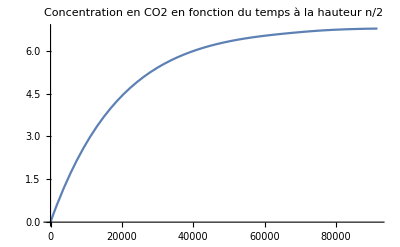

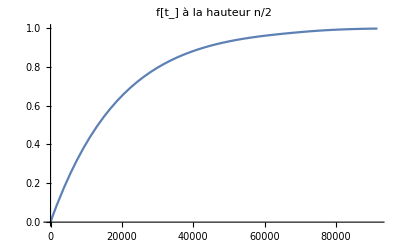

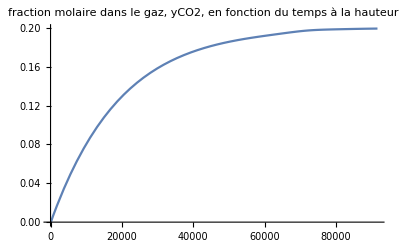

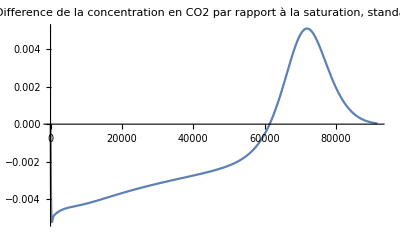

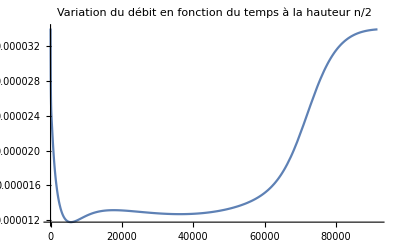

```mathematica
Γ=1000; (*position dans la colonne*)
e[t_]=Cco2[n/2][t]/.sol;
f[t_]=(Cco2[n/2][t])/(Hco2 Patm yco2[0][t])/.sol;
g[t_]=yco2[n/2][t]/.sol;
h[t_]= (Hco2 Patm yco2[n/2][t]-Cco2[n/2][t])/(Hco2 Patm yco2[0][t])/.sol;
k[t_]=Fg[n/2][t]/.sol;
Plot[e[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"Concentration en CO2 en fonction du temps à la hauteur n/2"]
Plot[f[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"f[t_] à la hauteur n/2"]
Plot[g[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"fraction molaire dans le gaz, yCO2, en fonction du temps à la hauteur n/2"]
Plot[h[t],{t,0,ψ τcg},PlotRange->All,PlotLabel->"Difference de la concentration en CO2 par rapport à la saturation, standardisé"]
Plot[k[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"Variation du débit en fonction du temps à la hauteur n/2"]
(*,PlotLabel->"Variation de la fraction molaire à mi-hauteur en fonction du temps",AxesLabel->{"Temps en seconde","Fraction molaire"},Frame->True,PlotRange->All,FrameStyle->Directive[Thick,Black],GridLines->Automatic]*)
```

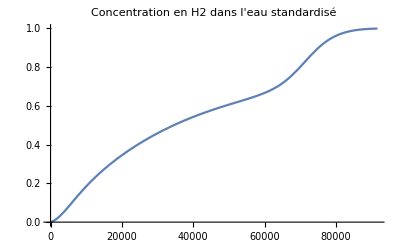

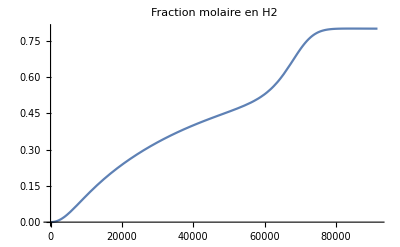

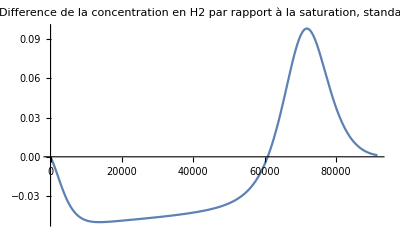

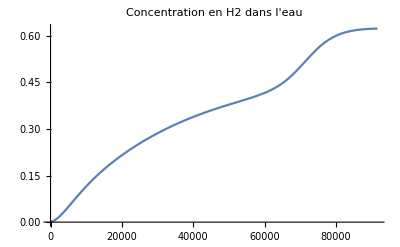

```mathematica
i[t_]=(Ch2[n/2][t])/(Hh2 Patm yh2[0][t])/.sol;
j[t_]=yh2[n/2][t]/.sol;
l[t_]= (Hh2 Patm yh2[n/2][t]-Ch2[n/2][t])/(Hh2 Patm yh2[0][t])/.sol;
m[t_]=Ch2[n/2][t]/.sol;
Plot[i[t],{t,0,ψ τcg},PlotRange->All, PlotLabel->"Concentration en H2 dans l'eau standardisé"]
Plot[j[t],{t,0,ψ τcg},PlotRange->All,PlotLabel->"Fraction molaire en H2"]
Plot[l[t],{t,0,ψ τcg},PlotRange->All,PlotLabel->"Difference de la concentration en H2 par rapport à la saturation, standardisé"]
Plot[m[t],{t,0,ψ τcg},PlotRange->All,PlotLabel->"Concentration en H2 dans l'eau"]
```

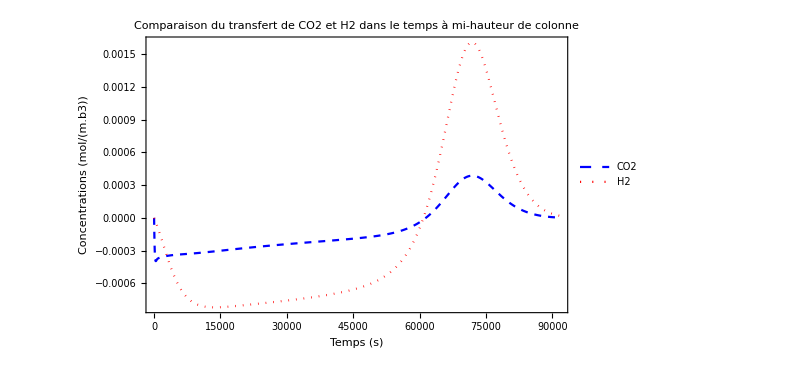

```mathematica
Plot[{Ap klco2 (Hco2 Patm yco2[n/2][t]-Cco2[n/2][t])/. sol,Ap klh2 (Hh2 Patm yh2[n/2][t]-Ch2[n/2][t])/. sol},{t,0,ψ τcg},PlotStyle->{Directive[Blue,Dashed],Directive[Red,Dotted]},(*Couleurs et styles différents pour les deux fonctions*)PlotLegends->Placed[{"CO2","H2"},{Scaled[{0.02,0.95}],{Left,Top}}],(*Positionnement de la légende*)
Frame->True,(*Activation du cadre*)
PlotRange->All,
FrameLabel->{"Temps (s)","Concentrations (mol/(m.b3))"},(*Étiquettes des axes*)
FrameStyle->Directive[Black,Thick],(*Style du cadre*)
PlotLabel->"Comparaison du transfert de CO2 et H2 dans le temps à mi-hauteur de colonne",(*Titre du graphique*)
BaseStyle->{FontSize->14},(*Taille de police*)
AxesStyle->Directive[Black,Thick],(*Style des axes*)
ImageSize->600 (*Taille de l'image*)]
```

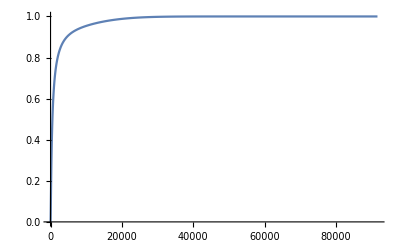

```mathematica
z[t_]=yh2[2][t]+yco2[2][t]/.sol;
Plot[z[t],{t,0,ψ τcg}, PlotRange->All]
```